# On-axis Digital Holography

AUTHOR: VICTORIA GÓMEZ BIFANTE

## CASE 1 - DISTANCE Z= 0 BETWEEN THE OBJECT AND HOLOGRAMAS

```mathematica
ClearAll[f]
```

## DATA

### Wavelength

```mathematica
λ = 500*10^(-6); (*mm*)
```

### Reference and Object wave

```mathematica
R[α_, β_, ϕR_] := Exp[ⅈ ϕR]; (*reference wave*)
Obj[α_,β_,ϕ_] := Exp[ⅈ ϕ UnitTriangle[Sqrt[α^2 + β^2]/0.5]]; (*object wave*)
```

### Interference

```mathematica
U1[α_,β_,ϕ_]:= Abs[Obj[α,β,ϕ] + R[α,β,0]]^2;
U2[α_,β_,ϕ_]:= Abs[Obj[α,β,ϕ] + R[α,β,π/2]]^2;
U3[α_,β_,ϕ_]:= Abs[Obj[α,β,ϕ] + R[α, β,π]]^2;
```

### Reconstructed wave

```mathematica
U[α_,β_,ϕ_]:= ((1+ⅈ)U1[α,β,ϕ]-2U2[α,β,ϕ]+(1-ⅈ)U3[α,β,ϕ])/(4ⅈ);
```

## RESULTS & GRAPHS

```mathematica
colorf[val_, maxval_]:=GrayLevel[(Rescale[val,{0,maxval}])]&;
colorbar[val_,maxval_]:= BarLegend[{GrayLevel[(Rescale[val,{0,maxval}])]&,{0,maxval}}];
```

### Original wave’s phase

-Graphics-

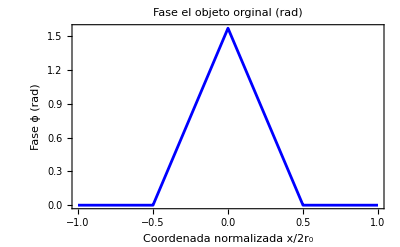

```mathematica
DensityPlot[Arg[Obj[α, β, π/2]],{ α, -1, 1}, {β, -1, 1}, Exclusions->None, PlotRange->All, PlotPoints->300, PlotLabel->"Representación de la fase del objeto (rad).", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, ColorFunctionScaling->False, ColorFunction->colorf[#1, 2π ], PlotLegends->colorbar[#1, π/2]]
Plot[Arg[Obj[α, 0, π/2]], {α, -1, 1},  Exclusions->None, PlotRange->All, PlotPoints->300, PlotLabel->"Fase el objeto orginal (rad)", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Fase ϕ (rad)"}, GridLines->{None, {π/2}}, PlotStyle->Blue]
```

### Holograms

-Graphics-

-Graphics-

-Graphics-

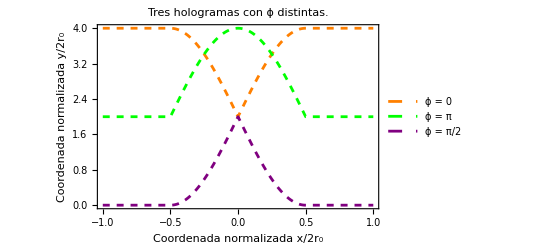

```mathematica
DensityPlot[U1[α, β, π/2],{ α, -1, 1}, {β, -1, 1}, Exclusions->None, PlotRange->All, PlotPoints->300, PlotLabel->"Intensidad para ϕ = 0 (u.a).", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, ColorFunctionScaling->False, ColorFunction->colorf[#1, 4 ], PlotLegends->colorbar[#1, 4]]
DensityPlot[U2[α, β, π/2],{ α, -1, 1}, {β, -1, 1}, Exclusions->None, PlotRange->All, PlotPoints->300, PlotLabel->"Intensidad para ϕ = π/2 (u.a).", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, ColorFunctionScaling->False, ColorFunction->colorf[#1, 4 ], PlotLegends->colorbar[#1, 4]]
DensityPlot[U3[α, β, π/2],{ α, -1, 1}, {β, -1, 1}, Exclusions->None, PlotRange->All, PlotPoints->300, PlotLabel->"Intensidad para ϕ = π (u.a).", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, ColorFunctionScaling->False, ColorFunction->colorf[#1, 4 ], PlotLegends->colorbar[#1, 4]]
Plot[{U1[α, 0, π/2],U2[α, 0, π/2],U3[α, 0, π/2]}, { α, -1, 1}, Exclusions->None, PlotRange->All, PlotPoints->300, PlotLabel->"Tres hologramas con ϕ distintas.", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, PlotLegends->{"ϕ = 0", "ϕ = π", "ϕ = π/2"}, PlotStyle->{{Dashed, Orange}, {Dashed, Green}, {Dashed, Purple}}]
```

### Reconstructed wave’s phase

-Graphics-

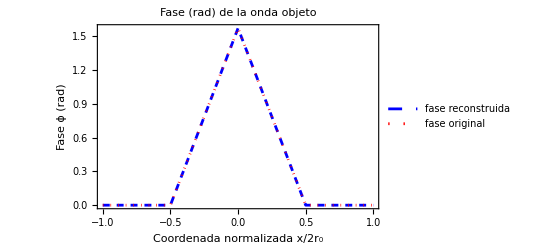

```mathematica
DensityPlot[Arg[U[α, β, π/2]],{ α, -1, 1}, {β, -1, 1}, Exclusions->None, PlotRange->All, PlotPoints->300, PlotLabel->"Representación de la fase del objeto (rad).", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, ColorFunctionScaling->False, ColorFunction->colorf[#1, 2π ], PlotLegends->colorbar[#1, π/2]]
Plot[{Arg[U[α, 0, π/2]], Arg[Obj[α, 0, π/2]]}, {α, -1, 1},  Exclusions->None, PlotRange->All, PlotPoints->300, PlotLabel->"Fase (rad) de la onda objeto", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Fase ϕ (rad)"}, PlotLegends->{"fase reconstruida", "fase original"}, PlotStyle->{{Dashed, Blue}, {Dotted, Red}}, FrameTicks->{{Automatic,{{π/2,"π/2"}}},{Automatic,None}}, GridLines->{None,{π/2}}]
```

## CASE 2 - DISTANCE Z = 500 (mm) BETWEEN THE OBJECT AND HOLOGRAMAS

## DATA

### Spatial and frequency dimension

```mathematica
Δα = 0.05; (*distance between points*)
atr = Table[Obj[α, β, π/2], {α, -5, 5, Δα}, {β, -5, 5, Δα}]; (*aliasing effect*)
Datr = Dimensions[atr][[1]];(*spacial coordenates*)
fatr = Fourier[N[atr]]; (*frequency coordenates*)
```

### Transfer function

```mathematica
H[u_, v_, z_] := Exp[-ⅈ π  λ z(u^2 + v^2)];
```

### Wave propagation (z = 0 to z = 500 mm)

```mathematica
fpropagation = Table[H[u, v, 500], {u, -1/(2 Δα), 1/(2 Δα) - 1/(Datr Δα), 1/(Datr Δα)}, {v, -1/(2Δα), 1/(2Δα)- 1/(Datr Δα), 1/(Datr Δα)}]; 
fp = Transpose[RotateRight[Transpose[RotateRight[fpropagation, Floor[(Datr + 1)/2]]], Floor[(Datr + 1)/ 2]]];
fpwave = fatr*fp; (*frequency dimension*)
propagatedwave = InverseFourier[N[fpwave]]; (*spatial dimension*)
```

### Wave propagation (z = 500 mm to z = 0)

```mathematica
returnwave= Fourier[N[propagatedwave]]; 
freturn = Table[H[u, v, -500], {u, -1/(2 Δα), 1/(2 Δα) - 1/(Datr Δα), 1/(Datr Δα)}, {v, -1/(2Δα), 1/(2Δα)- 1/(Datr Δα), 1/(Datr Δα)}];
fr = Transpose[RotateRight[Transpose[RotateRight[freturn, Floor[(Datr + 1)/2]]], Floor[(Datr + 1)/ 2]]];
rwave = returnwave * fr;
wave = Fourier[N[rwave]];
```

## RESULTS & GRAPHS

### Original wave’s phase (z = 0)

```mathematica
ArrayPlot[Arg[atr], PlotLabel->"Representación de la fase del objeto (rad).", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, ColorFunctionScaling->False, ColorFunction->colorf[#1, 2π], PlotLegends->colorbar[#1, π/2]]
```

-Graphics-

### Aliasing effect

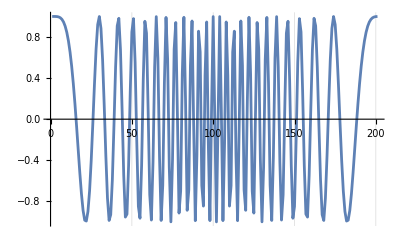

```mathematica
ListPlot[Re[fr[[1]]], PlotRange->All, PlotRange->All, Joined->True, GridLines->{301,None}]
```

### Reconstructed wave’s phase (z = 500 mm)

```mathematica
ArrayPlot[Abs[propagatedwave]^2, PlotLabel->"Intensidad (u.a) del objeto en z = 500 mm.", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, ColorFunctionScaling->False, ColorFunction->colorf[#1, 2 π], PlotLegends->colorbar[#1, π/2]]
ArrayPlot[Arg[propagatedwave], PlotLabel->"Fase (rad) del objeto en z = 500 mm.", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, ColorFunctionScaling->False, ColorFunction->colorf[#1, 2 π], PlotLegends->colorbar[#1, π/2]]
```

-Graphics-

-Graphics-

### Reconstructed wave’s phase (z = 0)

-Graphics-

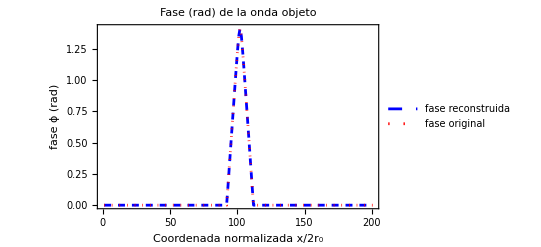

```mathematica
ArrayPlot[Arg[wave], PlotLabel->"Intensidad (u.a) del objeto en z = 500 mm.", Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "Coordenada normalizada y/2r_0"}, ColorFunctionScaling->False, ColorFunction->colorf[#1, 2 π], PlotLegends->colorbar[#1, 2 π]]
ListPlot[{Arg[wave][[Floor[(Datr + 1)/2]]], RotateRight[Arg[atr][[Floor[(Datr-1)/2]]], 1]}, Joined->True, PlotRange->All, PlotLabel->"Fase (rad) de la onda objeto",  Frame->True, FrameLabel->{"Coordenada normalizada x/2r_0", "fase ϕ (rad)"}, PlotLegends->{"fase reconstruida", "fase original"}, PlotStyle->{{Dashed, Blue}, {Dotted, Red}}, FrameTicks->{{Automatic,{{π/2,"π/2"}}},{Automatic,None}}, GridLines->{None,{π/2}}]
```